Basic Mathematica Tutorial
Jon Simon

First Things first, let’s learn to make some variables. We will create a variable called x and set it to 41:

```mathematica
x=41
```

To make the above cell “evaluate” (that is, execute as code), you must press SHIFT-ENTER will on top of that cell; just pressing ENTER will insert a newline! TRY BOTH!

Notice that Mathematica returned 41 as output. This occurred because we did not put a semicolon at the end of the line, which tells mathematica to SUPPRESS the result of the computation, like so:

```mathematica
y=37;
```

Running that code does not result in any return value!

Lets jump right into using mathematica in more powerful ways. Suppose I want to compute an indefinite integral of x Sin[x^2]. Run the next line of code:

```mathematica
Integrate[x Sin[x^2],x]
```

This is our first lesson in the frustrations of Mathematica. The above code did not work, but you can see that there are 41’ s where there should be x’ s! This says that x has been set to 41, which is actually our fault :( 
There are two ways out of this dilemma.
(1) When you have a confusing problem, the first thing to do is reset Mathematica’s memory by going up to the EVALUATION menu, and clicking QUIT KERNEL. This makes Mathematica forget about all prior assignments and start from scratch.
(2) If you do not want mathematica to forget about everything, but just about, say, x, then try:

```mathematica
x=.
```

Please choose one of these options, implement it, and then try again:

```mathematica
Integrate[x Sin[x^2],x]
```

Now it should have worked! Let’s examine that line of code a bit more carefully. Integrate takes two arguments, the first of which is the function to integrate, and the second of which is the variable of integration. If you want to perform a definite integral, try this form:

```mathematica
Integrate[x Sin[x^2],{x,a,b}]
```

Suppose we want to verify that -1/2 Cos[x^2] is actually the anti-derivative of x Sin[x^2], let’s ask Mathematica to take a derivative:

```mathematica
D[-1/2 Cos[x^2],x]
```

Another interesting aside for you : How did I generate x^2, rather than x^2? The trick is to press CTRL-6 rather than SHIFT-6; this generates a raised exponent. A similar trick works for CTRL-/, which produces nice looking fractions, and for CTRL-2, which produces a nice square root. More generally, these formatting tools can be accessed under the PALETTES menu at the top of the screen, but they are purely aesthetic!

Now imagine that I would like to know the Taylor expansion of x Cos[x^2] about x=0:

```mathematica
u=Series[x Cos[x^2],{x,0,5}]
```

```mathematica
It will be awkward to work with this expression with that extra O[x]^6 on the end. The Normal command removes it, and can be implemented either as Normal[Series[x Cos[x],{x,0,5}]] or u//Normal  Try one!
```

Series takes two arguments, the first is the function you’d like the taylor expansion of, and the second argument is a list whose first element is what variable to taylor expand with respect to, the second argument is what value of the variable to taylor expand around, and the third argument to what order in the variable to compute the taylor expansion.

So this brings us to a new question: what is a list?!
   A list is an ordered array of numbers, variables, and other lists. Here are some examples. Go ahead and execute them!

```mathematica
x=14; (*THIS IS A COMMENT! IT DOES NOT EVALUATE TO ANYTHING AND LETS ME BE VERBOSE! *)
l1={1,2,3};
l2={x,1,4};
l3={jon,4,31};
l4={l1,37,l2,l2};
```

It is instructive to ask Mathematica what  each list is. To do that, just enter the name of a list below, and evaluate.   Try it for each list! Notice that l2 contains the value of x, rather than its name! l3, on the other hand, just contains “jon”, since that variable has not been assigned a value. l4 contains full lists as elements.

If I want to know what the third element of l4 is, I type  l4[[3]]  Try it!

Suppose that what I’d actually like to do is change the value of l4[[3]] to 37. I type l4[[3]] = 37 Try that, and then ask mathematica to print out l4 again.

If I have a complicated expression and  I want to see if it can be simplified, the Mathematica commands are Simplify, and FullSimplify, depending upon how hard I want Mathematica to try. TRY IT! [Side Note: Mathematica is case-sensitive!!!]

```mathematica
FullSimplify[(x^2+4x +4)/(x+2)]
```

Suppose I have a symbolic expression that I want to evaluate with particular values of the variables. Try the line below. [Side Notes: Mathematica converts -> into →; to generate a ν, type ESCAPE nu ESCAPE]

```mathematica
ν(1+v/c)/(1-v/c)/.{v->10^7 m/s,c->3 10^8 m/s,ν->100. hz}
```

The code within the the braces is a list of “replacement rules,” and the /. tells mathematica to apply the replacement rules after the /. the expression before the /.

Suppose I want to make a plot:

```mathematica
Plot[x^2 Cos[x^2]Exp[-1/4 x^2],{x,-15,15}]
```

That plot was ugly. Let’s make sure that mathematica plots everything!

```mathematica
Plot[x^2 Cos[x^2]Exp[-1/4 x^2],{x,-15,15},PlotRange->All]
```

Much better!

Suppose I want to make a 3D Plot:

```mathematica
Plot3D[Exp[-(x^2+y^2)/10]Cos[x^2+y^2],{x,-5,5},{y,-5,5},PlotRange->All]
```

This is too jagged! Let’s add more points to the plot:

```mathematica
Plot3D[Exp[-(x^2+y^2)/10]Cos[x^2+y^2],{x,-5,5},{y,-5,5},PlotRange->All,PlotPoints->40]
```

That is very pretty!

Suppose I want to find the eigenvectors and eigenvalues of a matrix. First let’s define the matrix as a list of lists:

```mathematica
M={{0,2,0},{2,0,0},{0,0,1/2}};
```

Now Let’s compute its eigenvectors and eigenvalues:

```mathematica
Eigensystem[M]
```

{{-2,2,1/2},{{-1,1,0},{1,1,0},{0,0,1}}}

The first element of the result is a list of eigenvalues, while the second element of the result is a list of corresponding eigenvectors.

It is sometimes better to ask Mathematica not to do analytic computations by making the argument numeric. To do this, we add the N[] command around M, which turns it into a numeric matrix:

```mathematica
V=N[M]
Eigensystem[V]
```

Notice that while the eigenvalues are the same whether we compute analytically or numerically, the eigenvectors are differently normalized!

Mathematica is also capable of computing eigenvectors/values of totally symbolic matrices, though these can be extremely messy. Let’s pick a simple example, corresponding to two masses coupled together by springs, each separately connected to a wall:

```mathematica
EVs=Eigensystem[Inverse[{{m1,0},{0,m2}}].{{k+kc,-kc},{-kc,k+kc}}]
```

if we plug in some actual values it will be clearer what is going on:

```mathematica
EVs/.{k->1.,m1->1.,m2->1.,kc->.1}
```

To make this work, we made use of the Inverse command, which computes a matrix inverse, and the . command, which implements matrix multiplication.

Let’s get fancy now! I want to plot the eigenvalues of the above matrix as a function of m2; I should see an avoided crossing when it is equal to k1!

```mathematica
Plot[EVs[[1]]/.{k->1.,m1->1.,kc->.1},{m2,.1,2}]
```

Mathematica can solve differential equations:

```mathematica
DSolve[{y''[x]==-y[x],y[0]==1,y'[0]==0},y[x],x]
```

And it can solve systems of differential equations

```mathematica
DSolve[{x'[t]==v[t],v'[t]==-k/m x[t],x[0]==1,v[0]==0},{x[t],v[t]},t]
```

It can also numerically solve differential equations:

```mathematica
soln=NDSolve[{y''[x]==-Sin[y[x]]-.1y'[x],y[0]==0,y'[0]==2.204},y[x],{x,0,50}]
Plot[y[x]/.soln[[1]],{x,0,50},PlotRange->All]
```

This solution looks super-weird! Let us manipulate it to see if we can figure out what is going on!

```mathematica
Manipulate[
Module[{soln=NDSolve[{θ''[t]==-Sin[θ[t]]-.1θ'[t],θ[0]==0,θ'[0]==yi},θ[t],{t,0,50}]},
Plot[θ[t]/.soln[[1]],{t,0,50},PlotRange->{-10,10}]],{yi,0,3}]
```

This is messy, let’s break it down! The manipulate command runs its argument for a range of a parameter that you can control with a slider!

```mathematica
Manipulate[Plot[Exp[-x^2]Cos[β x],{x,-3,3},PlotRange->{-1,1}],{{β,2},0,10}]
```

The module command allows me to execute a whole block of code, {defining variables within braces only within the local scope} (if this bit doesn’t mean anything to you, ignore it), and return only the last element:

```mathematica
x=Module[{y=4},z=Cos[x];Cos[z]+.1]
```

You have probably noticed by now that functions take their parameters inside of brackets, rather than inside of perentheses! Let’s define a function, just for fun:

```mathematica
f[x_]:=Cos[x]+ArcTan[x];
f[3]
N[f[3]]
f[3.]
```

Notice that I have used delayed assignment := rather than assignment =    . This is because I want to be sure that this assignment uses whatever the value of x that I pass into f is, and not the value of x at the time when I run the above line of code! Also notice that there is an underscore after x; this is for pattern matching, and is always used in function definitions! As you can see, there is a lot of richness under mathematica’s hood that we are skipping. Don’t worry about it for now, and just be sure to use those underscores!

Let’s now try to do some curve fitting/data manipulation!

First we generate some random data:

```mathematica
jRand[]=RandomReal[]-.5;
c0=jRand[]*3.;
s0=jRand[]*.5;
A0=RandomReal[]*20;
c0=jRand[]*5;
g0=jRand[]*4;
tdat=Table[{x,c0+s0  x+A0/(1+((x-c0)/(g0/2))^2)+(RandomReal[]-.5).4},{x,-15,20,.1}];
```

Let us see what the data looks like:

```mathematica
ListPlot[tdat]
```

Now we pick a fit form and play with guess parameters by hand until the data and fit form look similar:

```mathematica
FitForm=d+α(x-x0)+β/(1+((x-x0)/(γ/2))^2);
GuessParms={d->-1.,α->-.12,x0->-1.,γ->1.,β->7};
Show[ListPlot[tdat,PlotRange->All],Plot[FitForm/.GuessParms,{x,-15,20},PlotRange->All]]
```

The code within the the braces is a list of “replacement rules,” and the /. tells mathematica to apply the replacement rules after the /. the expression before the /.

Now we call the fitting routine “FindFit” with our guess as input!

```mathematica
FitParms=FindFit[tdat,FitForm,{{d,-1},{α,-.12},{x0,-1},{γ,1.},{β,7.}},x]
Show[ListPlot[tdat,PlotRange->All],Plot[FitForm/.FitParms,{x,-15,20},PlotRange->All]]
```

et voila!

Shall we try to import some data and fit to that? The next line of code downloads a file from my group’s website! You could also manually download it with your web-browser, put it in the same folder as this tutorial, and then use:
SetDirectory[NotebookDirectory[]];indata=Import[“TutorialData.csv”]

```mathematica
indata=Import["http://simonlab.uchicago.edu/TutorialData.csv"];
```

Let us see what this data looks like:

```mathematica
ListPlot[indata,PlotRange->All]
```

OK! So we can fit to this! Let’s define a guess function, and tweak the parameters until they are about right, and then run the fit routine!

```mathematica
FitForm=A Exp[-α (x-x00)^2]Sin[ β x+ϕ];
GuessParms={A->1.1,α->.1,β->2π,ϕ->1.5,x00->2};
Show[ListPlot[indata,PlotRange->All],Plot[FitForm/.GuessParms,{x,-20,20},PlotRange->All]]
```

Now that we are close, let’s fit to it and plot the results:

```mathematica
FitParms=FindFit[indata,FitForm,{{A,1.},{α,.1},{β,2π},{ϕ,0},{x00,2}},x]
Show[ListPlot[indata,PlotRange->All],Plot[FitForm/.FitParms,{x,-20,20},PlotRange->All]]
```

What if I want to sort a list?
Well first let’s make a list to sort:

```mathematica
data=Table[RandomReal[],{j,1,100}];
```

and plot its values

```mathematica
ListPlot[data]
```

We could sort it by using the sort routine:

```mathematica
sortedlist=Sort[data];
```

```mathematica
ListPlot[sortedlist]
```

Or we could do it ourselves, to learn about If statements, and While loops. We will implement the bubble sort, an extremely inefficient but simple to work with sort routine.

```mathematica
sortedlist=data;
Done=False;
While[Done==False,
Done=True;
For[j=1,j≤Length[sortedlist]-1,
If[sortedlist[[j]]>sortedlist[[j+1]],
tmp=sortedlist[[j]];sortedlist[[j]]=sortedlist[[j+1]];sortedlist[[j+1]]=tmp;
Done=False,
True
];
j=j+1
]
]
```

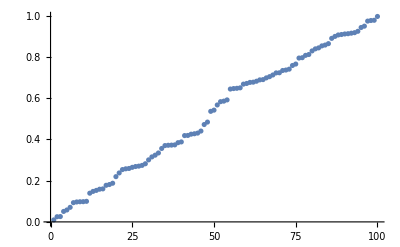

```mathematica
ListPlot[sortedlist]
```

It worked!!

That is it! What else would you like to learn about in the remaining time!?
While you think about it, try these:

```mathematica
MySong=Import["http://simonlab.uchicago.edu/TutorialSong.mid"];
Sound[MySong]
```

```mathematica
CurrentImage[]
```

Other things I could teach you about if you want
Making 2D Graphics
Making 3D Graphics
Making Animations
Solving Partial Differential Equations Numerically/Analytically
Looping Structures, and more general programming techniques